### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem set 2

### 2.2 Damped pendulum e)

```mathematica
xDot[x_,y_,σ_]:=y
yDot[x_,y_,σ_]:=-Sin[x]-σ y
```

```mathematica
Solve[{xDot[x,y,σ] == 0, yDot[x,y,σ]==0}]
```

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

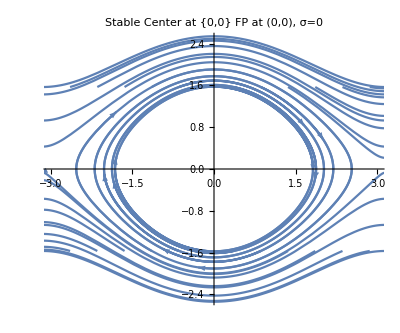

```mathematica
minx=-π;
miny=-π/2;
maxx=π;
maxy=π/2;
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{0}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{-3,3},{-2.5,2.5}},
PlotLabel->"Stable Center at {0,0}\nFP at (0,0), σ=0"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

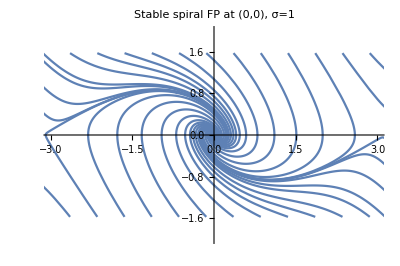

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{1}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{-3,3},{-2,2}},
PlotLabel->"Stable spiral\nFP at (0,0), σ=1"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

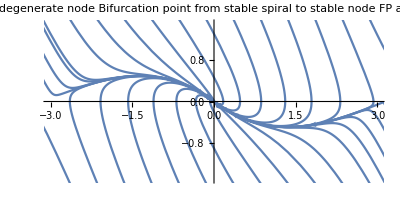

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{2}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{-3,3},{-1.5,1.5}},
PlotLabel->"Stable degenerate node\nBifurcation point from stable spiral to stable node\nFP at (0,0), σ=2"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

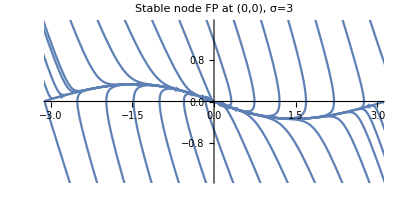

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{3}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{-3,3},{-1.5,1.5}},
PlotLabel->"Stable node\nFP at (0,0), σ=3"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

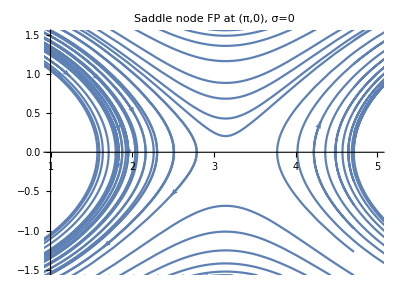

```mathematica
minx=-π/2;
miny=-π/2;
maxx=3π/2;
maxy=π/2;
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{0}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotLabel->"Saddle node\nFP at (π,0), σ=0"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

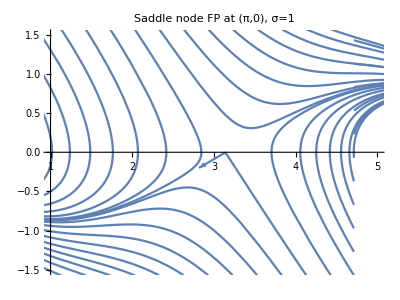

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{1}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotLabel->"Saddle node\nFP at (π,0), σ=1"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

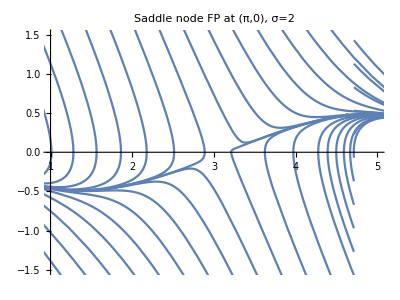

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{2}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotLabel->"Saddle node\nFP at (π,0), σ=2"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```

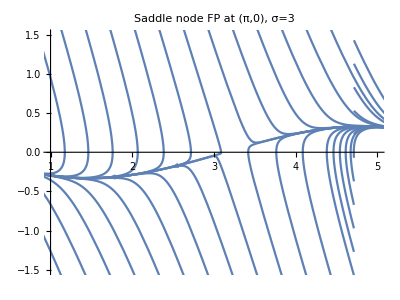

```mathematica
sol[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{3}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotLabel->"Saddle node\nFP at (π,0), σ=3"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{p}]
```